```mathematica
ap[f_]:=(f*x-D[f,x])/Sqrt[2];
```

```mathematica
am[f_]:=(f*x+D[f,x])/Sqrt[2];
```

```mathematica
sol=DSolve[am[v[x]]==0,v[x],x]
```

{{v[x]→ⅇ^(-x^2/2) C[1]}}

```mathematica
phi[0]=v[x]/.sol[[1]]
```

ⅇ^(-x^2/2) C[1]

```mathematica
intg:=Integrate[phi[0]^2, {x, -Infinity, Infinity}];
intg
```

√π C[1]^2

```mathematica
sol=Solve[intg==1,C[1]]
```

{{C[1]→-1/π^(1/4)},{C[1]→1/π^(1/4)}}

```mathematica
phi[0]=phi[0]/.sol[[2]]
```

(ⅇ^(-x^2/2))/π^(1/4)

```mathematica
Integrate[phi[0]^2, {x, -Infinity, Infinity}]
```

1

```mathematica
phi[n_]:=Together@ap[phi[n-1]]/Sqrt[n]
```

```mathematica
phi[2]
```

(ⅇ^(-x^2/2) (-1+2 x^2))/(√2 π^(1/4))

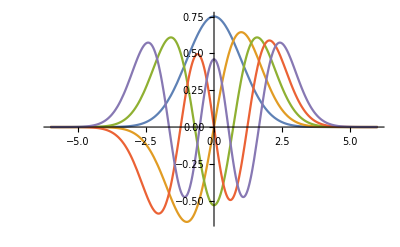

```mathematica
Plot[Evaluate@Table[phi[n],{n,0,4}], {x, -6, 6}]
```

```mathematica
Table[Integrate[phi[n]^2,{x,-Infinity,Infinity}],{n,0,4}]
```

{1,1,1,1,1}

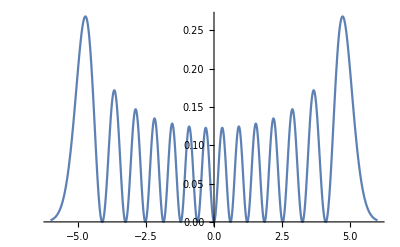

```mathematica
Plot[Evaluate[phi[13]^2],{x,-6,6}]
```